```mathematica
SetDirectory["C:/Users/serha/OneDrive/Masaüstü/MyRepo/master_thesis_MMT003/"];
```

```mathematica
datafull=Import["C:/Users/serha/OneDrive/Masaüstü/MyRepo/master_thesis_MMT003/data/csp_data.csv",HeaderLines->1];
```

```mathematica
Get["SingleNetworks-algorithm-package.wl"]
(* ?SingleNetworks`* *)
```

```mathematica
data=Table[Take[datafull,UpTo@i],{i,Ceiling@Range[13763.5,137635,13763.5]}];
```

```mathematica
Dimensions@data
```

{10}

fixed step size

```mathematica
AbsoluteTiming[widthdataintimewindowsFixedstep=snetworkdatabinnedintimewindows[5,20,10];]
```

{811.809,Null}

```mathematica
Dimensions@widthdataintimewindowsFixedstep
```

{3,10}

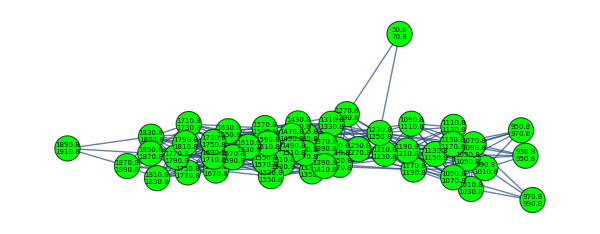
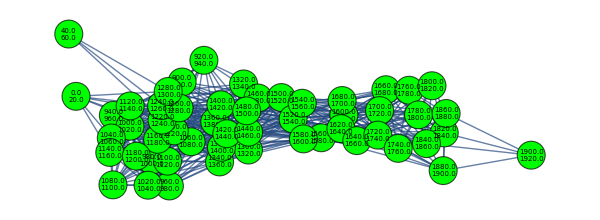
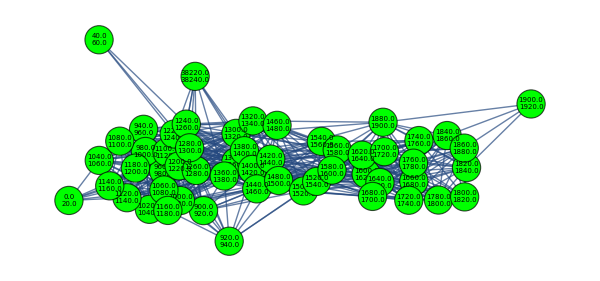
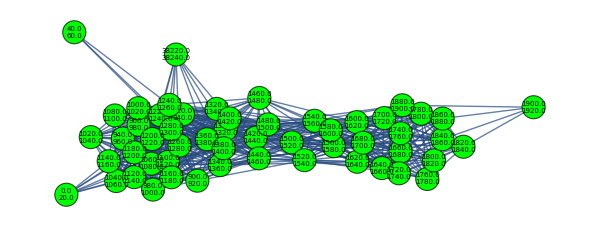
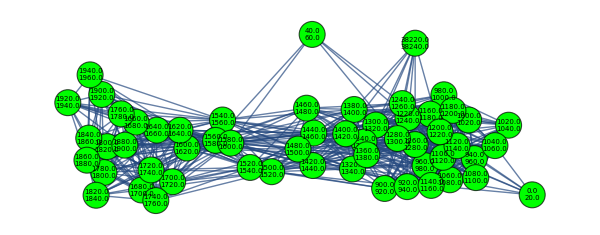
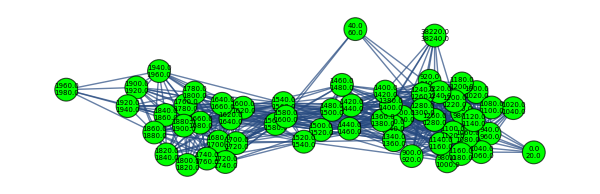
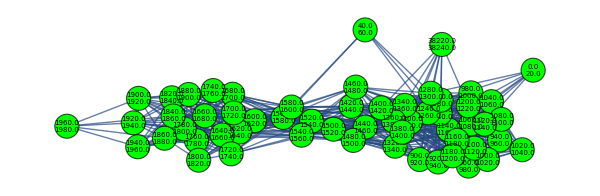
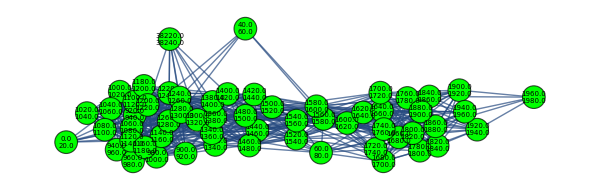
{{-Graphics-,50},{-Graphics-,53},{-Graphics-,54},{-Graphics-,54},{-Graphics-,56},{-Graphics-,57},{-Graphics-,57},{-Graphics-,58},{-Graphics-,58},{-Graphics-,58}}

```mathematica
Table[snetworkgraph[widthdataintimewindowsFixedstep[[1]][[i]],widthdataintimewindowsFixedstep[[2]][[i]],2,7,600,Green],{i,Range@10}]
```

```mathematica
thickness=networkdatabinned[6,0.01];
width=networkdatabinned[5,20];
```